# Gamma - ^163Lu shape transition

## Studying the shape transition with respect to the triaxiality parameter γ

```mathematica
gammas={17,18,19,20,21};
```

### (0,0) - formalism for bands

```mathematica
mois00={{77,24,4},{76,52,3},{76,52,3},{76,52,3},{77,48,3}};
v00={1.26,1.76,1.76,1.76,1.51};
```

### (1,0) - formalism for bands

```mathematica
mois10={{73,3,67},{73,3,67},{73,3,67},{73,3,67},{77,3,67}};
v10={7.26,6.76,6.51,6.26,6.01};
```

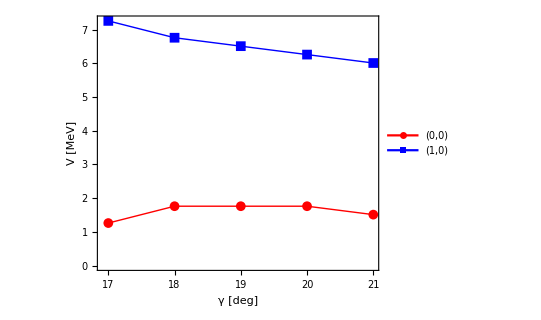

```mathematica
ListPlot[{Table[{gammas[[i]],v00[[i]]},{i,1,Length[gammas]}],Table[{gammas[[i]],v10[[i]]},{i,1,Length[gammas]}]},Joined->True,Frame->True,Axes->False,PlotStyle->{{Red,Thick},{Blue,Thick}},PlotMarkers->{Automatic,10},AspectRatio->0.8,FrameLabel->{"γ [deg]","V [MeV]"},PlotLegends->Placed[{"(0,0)","(1,0)"},{0.3,0.5}],LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},FrameStyle->Directive[Black,Thick]]
```

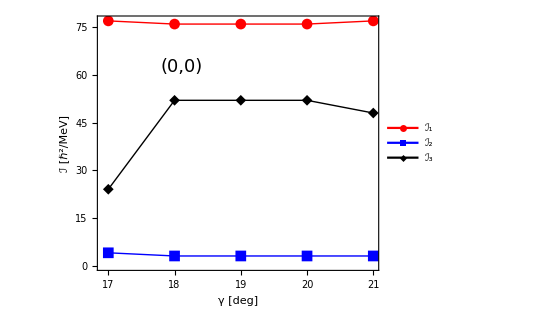

```mathematica
ListPlot[{Table[{gammas[[i]],mois00[[i,1]]},{i,1,Length[gammas]}],Table[{gammas[[i]],mois00[[i,3]]},{i,1,Length[gammas]}],Table[{gammas[[i]],mois00[[i,2]]},{i,1,Length[gammas]}]},Joined->True,Frame->True,Axes->False,PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick}},PlotMarkers->{Automatic,11},AspectRatio->0.8,FrameLabel->{"γ [deg]","ℐ [ℏ^2/MeV]"},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},FrameStyle->Directive[Black,Thick],PlotLegends->Placed[{"ℐ_1","ℐ_2","ℐ_3"},{0.3,0.3}],Epilog->Inset[Style["(0,0)",18,Italic,Black,FontFamily->"Times New Roman"],Scaled[{0.3,0.8}]]]
```

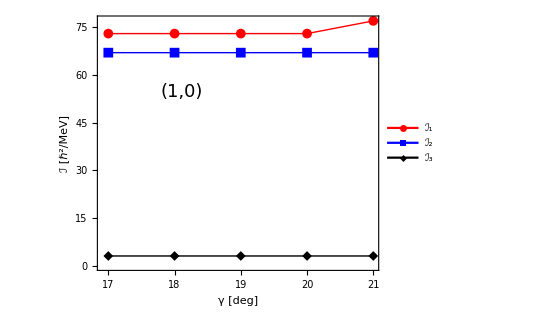

```mathematica
ListPlot[{Table[{gammas[[i]],mois10[[i,1]]},{i,1,Length[gammas]}],Table[{gammas[[i]],mois10[[i,3]]},{i,1,Length[gammas]}],Table[{gammas[[i]],mois10[[i,2]]},{i,1,Length[gammas]}]},Joined->True,Frame->True,Axes->False,PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick}},PlotMarkers->{Automatic,10},AspectRatio->0.8,FrameLabel->{"γ [deg]","ℐ [ℏ^2/MeV]"},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},FrameStyle->Directive[Black,Thick],PlotLegends->Placed[{"ℐ_1","ℐ_2","ℐ_3"},{0.3,0.3}],Epilog->Inset[Style["(1,0)",18,Italic,Black,FontFamily->"Times New Roman"],Scaled[{0.3,0.7}]]]
```

## Update - parallel approach

```mathematica
gammas={15,16,17,18,19,20,21,22,23,24,25};
v00={1.91,1.91,1.81,1.81,1.81,1.71,1.71,1.61,1.61,1.61,1.51};
v10={8.01,7.61,7.21,6.91,6.61,6.31,6.11,5.81,5.61,5.51,5.31};
mois00={{76,52,3},{76,52,3},{76,52,3},{76,52,3},{76,52,3},{76,52,3},{76,52,3},{76,51,3},{76,51,3},{76,52,3},{76,51,3}};
mois10={{73,3,67},{73,3,67},{73,3,67},{73,3,67},{73,3,67},{73,3,67},{73,3,67},{73,3,67},{73,3,67},{73,3,67},{73,3,67}};
```

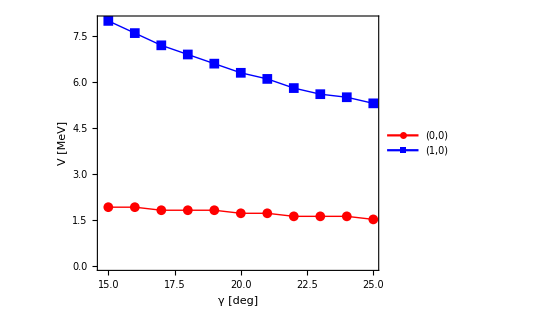

```mathematica
ListPlot[{Table[{gammas[[i]],v00[[i]]},{i,1,Length[gammas]}],Table[{gammas[[i]],v10[[i]]},{i,1,Length[gammas]}]},Joined->True,Frame->True,Axes->False,PlotStyle->{{Red,Thick},{Blue,Thick}},PlotMarkers->{Automatic,10},AspectRatio->0.8,FrameLabel->{"γ [deg]","V [MeV]"},PlotLegends->Placed[{"(0,0)","(1,0)"},{0.3,0.5}],LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},FrameStyle->Directive[Black,Thick]]
```